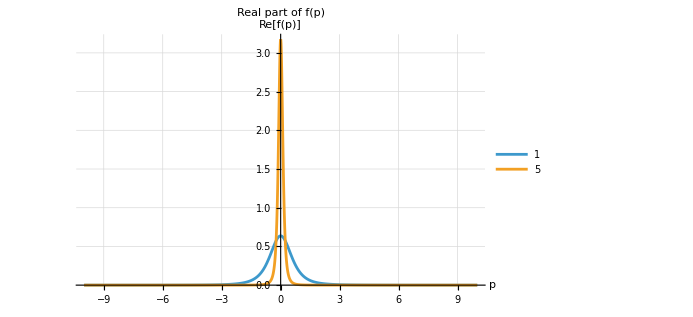

```mathematica
f[n_,p_]:=Sqrt[2 n/π]*((n p+I)^(n-1))/((n p-I)^(n+1))
Absf[n_,p_]:=Abs[Sqrt[2 n/π]*((n p+I)^(n-1))/((n p-I)^(n+1))]^2
(*List of n values*)
nList=Range[1,4];
nList={1,5};
Plot[Evaluate[Table[Re[Absf[n,p]],{n,nList}]],{p,-10,10},PlotLabel->"Real part of f(p)",AxesLabel->{"p","Re[f(p)]"},PlotRange->All,PlotLegends->Placed[nList,Below],GridLines->Automatic]
```

```mathematica
ψ[k_,p_]:=Module[{},Sqrt[2 k/π]/Sqrt[1-Exp[-2 π/k]]*(1/(p^2-k^2))*((p+k)/(p-k))^(I/k)];
Absψ[k_,p_]:=Abs[Module[{},Sqrt[2 k/π]/Sqrt[1-Exp[-2 π/k]]*(1/(p^2-k^2))*((p+k)/(p-k))^(I/k)]]^2;
ψintegral[kval_,ε_]:=Total[NIntegrate[Absψ[kval,p],{p,#1,#2}]&@@@{{-100,-kval-ε},{-kval+ε,kval-ε},{kval+ε,100}}]
```

1/10000000000

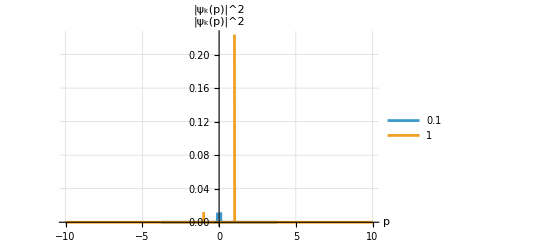

```mathematica
(*kList=Range[0.1,10,2];*)
kList={0.1,1};
ε=10^-4; (*Set small epsilon neighborhood around singularities*)
threshold=10^-10
(*Plot[Evaluate[Table[Re[ψ[k,p]],{k,kList}]],{p,-5,5},PlotLabel->"Real part of ψₖ(p)",AxesLabel->{"p","Re[ψₖ(p)]"},PlotRange->All,PlotLegends->Placed[kList,Below],GridLines->Automatic,RegionFunction->Function[{p,y},And@@Table[Abs[p-k]>ε&&Abs[p+k]>ε,{k,kList}]]]*)
Plot[Evaluate[Table[Re[Absψ[k,p]/ψintegral[k,10^-2ε]],{k,kList}]],{p,-10,10},PlotLabel->"|ψₖ(p)|^2",AxesLabel->{"p","|ψₖ(p)|^2"},PlotRange->All,PlotLegends->Placed[kList,Below],GridLines->Automatic,RegionFunction->Function[{p,y},And@@Join[Table[Abs[p-k]>ε&&Abs[p+k]>ε,{k,kList}],{y>threshold}]]]
```

```mathematica
ψintegral[5,10^-8]
```

ψintegral[5,1/100000000]

```mathematica
kval=5; (*Example k value*)
ε=10^-8; (*Small exclusion around the singularities*)

integral=Total[NIntegrate[Absψ[kval,p],{p,#1,#2}]&@@@{{-2kval,-kval-ε},{-kval+ε,kval-ε},{kval+ε,2kval}}]
```

1.14316×10^7

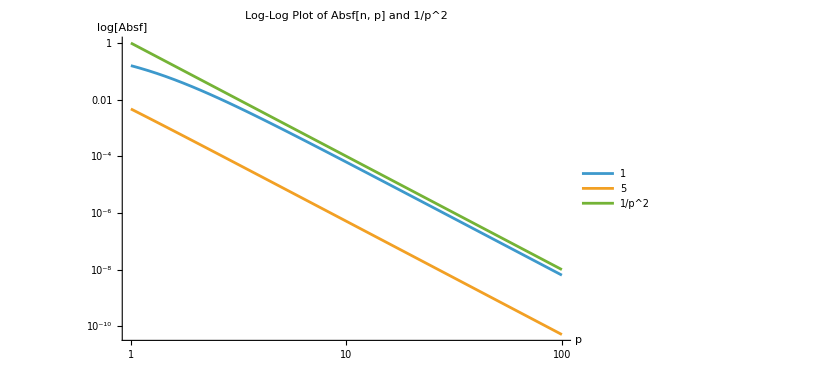

```mathematica
Absf[n_,p_]:=Abs[Sqrt[2 n/π]*((n p+I)^(n-1))/((n p-I)^(n+1))]^2

nList={1,5};

LogLogPlot[Evaluate[Table[Absf[n,p],{n,nList}]~Join~{1/p^4}],{p,1,100},(*Avoid p=0 since 1/p^2 blows up*)PlotLabel->"Log-Log Plot of Absf[n, p] and 1/p^2",PlotLegends->Placed[Join[ToString/@nList,{"1/p^2"}],Below],AxesLabel->{"p","log[Absf]"},PlotRange->All,GridLines->Automatic]
```

```mathematica
Table[{p,Absf[5,p]/(1/p^4)//N},{p,10,100,10}]
```

{{10,0.00508889},{20,0.00509194},{30,0.00509251},{40,0.0050927},{50,0.0050928},{60,0.00509285},{70,0.00509288},{80,0.00509289},{90,0.00509291},{100,0.00509292}}

```mathematica
Table[{p,Absf[1,p]/(1/p^4)//N},{p,10,100,10}]
```

{{10,0.624076},{20,0.633449},{30,0.635207},{40,0.635825},{50,0.636111},{60,0.636266},{70,0.63636},{80,0.636421},{90,0.636463},{100,0.636492}}